```mathematica
<<PCA.m

faces = LoadFaces[100];
flatFaces = FlattenImage /@ faces;
```

```mathematica
eigenfaces = Import["eigenfaces.csv", "CSV"]
```

{{-0.0134907,-0.0135818,-0.0144262,-0.0149469,-0.0151451,4890,-0.00136217,-0.00255911,-0.00356818,-0.00366761,-0.00401622},48,{1}}
 |  |  |  |

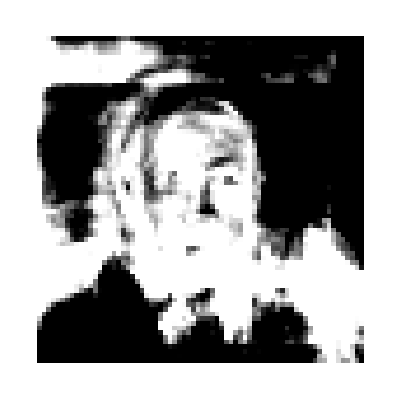

```mathematica
FormatFace[100 * eigenfaces[[8]]]
```

```mathematica
avg = N[Total[flatFaces]]/Length[flatFaces];
```

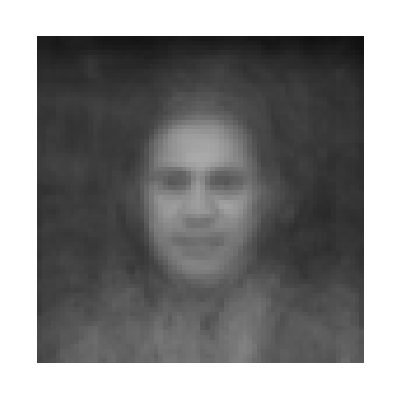
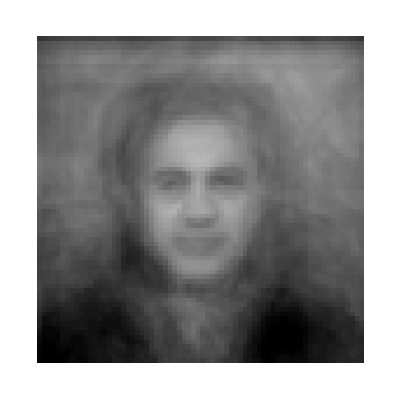
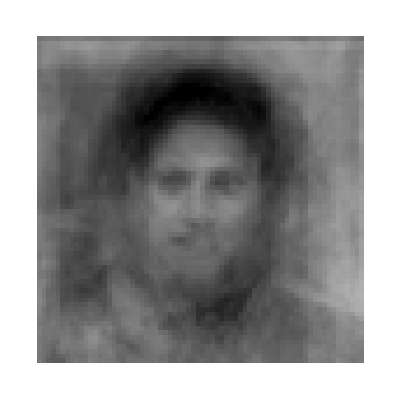
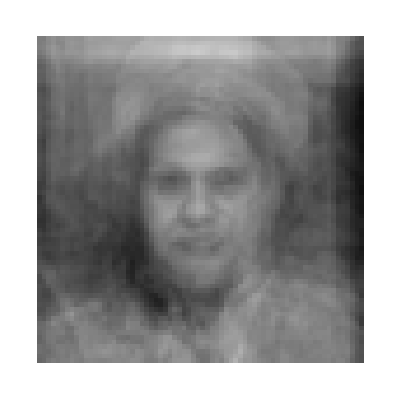
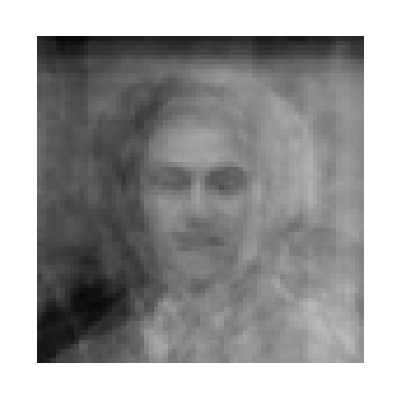
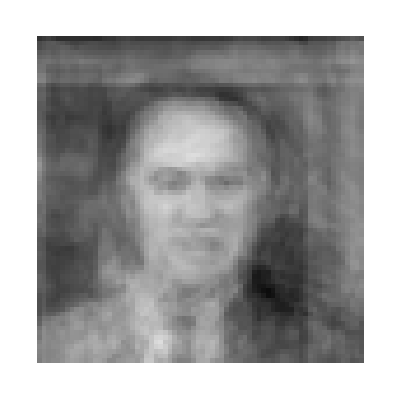
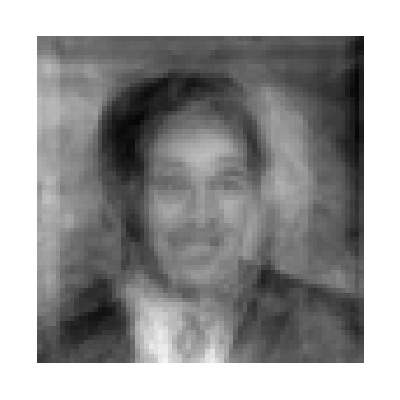
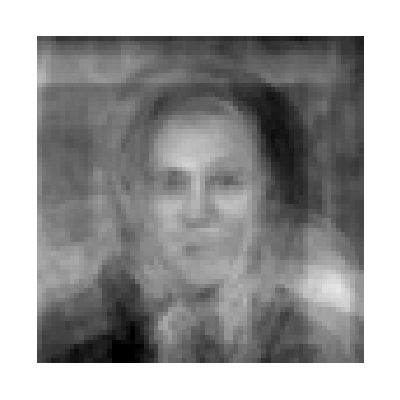

```mathematica
FormatFace /@ (Function[x,10 * x + avg ] /@ eigenfaces)
```